```mathematica
For[i=0,i<4,i++,Print[i]]
```

0

1

2

3

```mathematica
For[i=1,i<62,i++,z=i/10;g=1/Gamma[N[z]];Print[g]]
```

0.105114

0.217825

0.334273

0.450824

0.56419

0.671505

0.770383

0.858937

0.935779

1.

1.05114

1.08912

1.11424

1.12706

1.12838

1.11917

1.10055

1.07367

1.03975

1.

0.955579

0.907604

0.85711

0.805043

0.752253

0.699484

0.647381

0.596484

0.547239

0.5

0.455038

0.412547

0.372656

0.335435

0.300901

0.269032

0.239771

0.21303

0.188703

0.166667

0.146786

0.128921

0.112926

0.0986573

0.0859717

0.0747312

0.0648029

0.0560605

0.0483854

0.0416667

0.0358015

0.0306955

0.0262619

0.0224221

0.0191048

0.0162459

0.0137878

0.0116793

0.00987457

0.00833333

0.00701991

```mathematica
1/Gamma[1/10]
```

1/Gamma[1/10]

```mathematica
N[1/10]
```

0.1

```mathematica
1/Gamma[3]
```

1/2

```mathematica
z=9.31481481481
For[i=1,i<62,i++,k=i/10;g=z^k*(k-1)/Gamma[N[k]];Print[k,g]]
```

9.31481

1/10-0.118255

1/5-0.27229

3/10-0.457037

2/5-0.660432

1/2-0.860958

3/5-1.02474

7/10-1.10217

4/5-1.02407

9/10-0.697317

10.

11/10 1.22391

6/5 3.17042

13/10 6.08173

7/5 10.253

3/2 16.0393

8/5 23.8632

17/10 34.2218

9/5 47.6952

19/10 64.9537

286.7658

21/10 114.005

11/5 147.659

23/10 188.834

12/5 238.762

5/2 298.807

13/5 370.468

27/10 455.385

14/5 555.34

29/10 672.258

3808.207

31/10 965.399

16/5 1146.18

33/10 1353.04

17/5 1588.59

7/2 1855.55

18/5 2156.78

37/10 2495.19

19/5 2873.83

39/10 3295.77

43764.15

41/10 4282.15

21/5 4852.94

43/10 5479.71

22/5 6165.59

9/2 6913.66

23/5 7726.91

47/10 8608.25

24/5 9560.42

49/10 10586.

511687.5

51/10 12866.9

26/5 14126.3

53/10 15467.4

27/5 16891.6

11/2 18399.8

28/5 19993.

57/10 21671.4

29/5 23435.1

59/10 25283.8

627216.6

61/10 29232.4

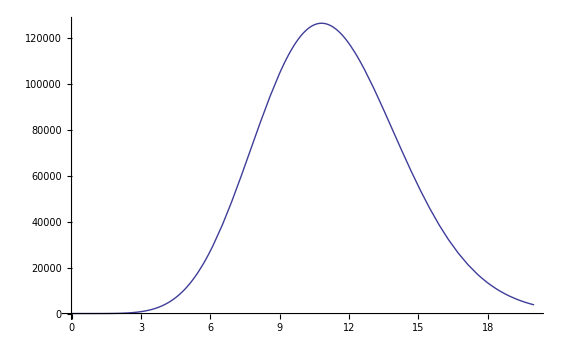

```mathematica
Plot[z^x*(x-1)/Gamma[x],{x,0,20}]
```

```mathematica
NIntegrate[z^x*(x-1)/Gamma[x],{x,0,1}]
NIntegrate[z^x*(x-1)/Gamma[x],{x,0,∞}]
Exp[-z]*NIntegrate[z^x*(x-1)/Gamma[x],{x,0,∞}]
Exp[-z]*NIntegrate[z^x*(x-1)/Gamma[x],{x,0,1}]
Exp[-z]*NIntegrate[z^x*(x-1)/Gamma[x],{x,1,∞}]
Exp[-z]*NIntegrate[z^x*(x-1)/Gamma[x],{x,1,60}]
Exp[-z]*NIntegrate[z^x*(x-1)/Gamma[x],{x,1,70}]
Exp[-z]*NIntegrate[z^x*(x-1)/Gamma[x],{x,1,80}]
Exp[-z]*NIntegrate[z^x*(x-1)/Gamma[x],{x,1,90}]
Exp[-z]*NIntegrate[z^x*(x-1)/Gamma[x],{x,1,100}]
Exp[-z]*NIntegrate[z^x*(x-1)/Gamma[x],{x,1,1000}]
```

```mathematica
-0.6302987518309
```

963210.

86.7658

-0.0000567772

86.7658

86.7658

86.7658

«1 more identical outputs»

```mathematica
86.76582495378688
```

```mathematica
86.76582495378659
```

86.7658

```mathematica
86.76582495379236
```

```mathematica
86.76582495414681
```

```mathematica
86.76582495380228
```

```mathematica
86.76582495378675
```

```mathematica
86.76582495378688
```

```mathematica
86.76582495378659
```

```mathematica
86.76582495378679
```

```mathematica
86.76576817662735
```

```mathematica
-0.0000567771740937604
```

```mathematica
86.76582495379236
```

```mathematica
N[1/Gamma[147]]
N[1/Gamma[149]]
N[1/Gamma[150]]
```

8.51066×10^-255

3.91187×10^-259

2.62541×10^-261